```mathematica
q[v_]:=0.5*Erfc[v/(√2)];
oneOverN[nd_, p_]:=1/(nd p) (1-(1-p)^nd);
oneOverN2[nd_, p_]:=NIntegrate[(1-p+p x)^(nd-1) (-Log[x]), {x, 0, 1.}];
gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w((k+b)-(1-beta/ns)w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=(k+b)-(1-beta/ns)w x;
g1NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, bkTmp, kFactor},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor = ndR oneOverN[nd, pUpdated];
bkTmp = k kFactor + b;
(-2. ⅇ^(-bla^2/2)  (bkTmp ns+bla (beta-ns) w)+(beta (-1+ns)+ns)√(2 π)w Erfc[bla/(√2)])/(2 ns w √(2 π))
];
g21NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, kFactor1, kFactor2, bkTmp1, bkTmp2},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor1 = ndR oneOverN[nd, pUpdated];
kFactor2 = ndR^2 oneOverN2[nd, pUpdated];
bkTmp1 = k kFactor1 + b;
bkTmp2 = k^2 kFactor2 + 2b k kFactor1 + b^2;
1./(2 ns^2)(ⅇ^(-bla^2/2) (beta-ns) √(2/π) w (2 bkTmp1 ns+bla (beta-ns) w)+(bkTmp2 ns^2+(beta-ns)^2 w^2) Erfc[bla/(√2)])
];
g22NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, kFactor1, bkTmp1},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor1 = ndR oneOverN[nd, pUpdated];
bkTmp1 = k kFactor1 + b;
1/(2 ns^2)(1/w^2 ⅇ^(-bla^2/2) √(2/π) (bkTmp1 ns+bla (beta-ns) w) (bkTmp1 bla ns+beta (2+bla^2) w-(2+2 beta+bla^2) ns w)+(2 beta^2-2 beta (2+beta) ns+(2+beta (2+beta)) ns^2) Erfc[bla/(√2)])
];
betaSolutionNonInt[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21NonInt[b, k, nd, ns, ndR, y, w]-2g1NonInt[b, k, nd, ns, ndR, y, w]+g22NonInt[b, k, nd, ns, ndR, y, w]/ns, {y,100}];
(*****************************************************************************)
```

```mathematica
tmpfunNonInt[b_, bk_, ndR_, nd_, ns_]:=Module[{k, beta, g1, g21, g22, g31, g32}, 
k = bk-b;
beta = betaSolutionNonInt[b, k, nd, ns, ndR, 1.]//Quiet; 
g1 = g1NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g21 = g21NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g22 = g22NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
{beta, g1, g21, g22}
];
```

```mathematica
paramsList = Import["/home/fangxu/BennaLab/dendrite_familiarity_detection/tmp_data/tmp.csv"];
paramsList//Dimensions
```

{85,5}

```mathematica
paramsFunTmp[nd_, ns_, b_, bk_, ndR_]:=Module[{beta}, 
beta = betaSolutionNonInt[b, bk-b, nd, ns, ndR, 1.]//Quiet; (*note that here we can't always set b=0, kappa = b+kappa *)
{nd, ns, bk, b, ndR, beta, 20240305}
];
tmpParams = ParallelTable[paramsFunTmp[paramsList[[idx, 4]],paramsList[[idx, 5]], paramsList[[idx, 1]], paramsList[[idx, 2]], paramsList[[idx, 3]]], {idx, 1, Length[paramsList]}];
```

```mathematica
paramsFunTmp[300, 200, 2.0, 3.5, 10]
```

{300,200,3.5,2.,10,3.8745,20240305}

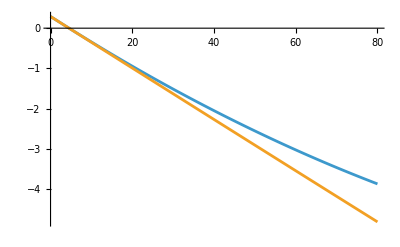

```mathematica
Clear["tmpfun"]
tmpfun2[y_, bk_, nd_, ns_, ndR_]:=g21NonInt[0.,bk,nd,ns,ndR,y,1.]-2 g1NonInt[0.,bk,nd,ns,ndR,y,1.]+1/ns g22NonInt[0.,bk,nd,ns,ndR,y,1.];
tmpfun1[y_, bk_, nd_, ns_, ndR_]:=g21NonInt[0.,bk,nd,ns,ndR,y,1.]-2 g1NonInt[0.,bk,nd,ns,ndR,y,1.];
nd=300;ns=200;bk=3.5;ndR=10;
Plot[{tmpfun2[y, bk, nd, ns, ndR], tmpfun1[y, bk, nd, ns, ndR]}, {y, 0, 80}]
```